```mathematica
ClearAll["Global`*"]
```

# Kadomtsev sawtooth

## The equilibrium and end state

First off, let’s put down some handy-dandy definitions for our equilibrium

```mathematica
q = q0 +  b*a^2;
Solq1 = Solve[q==1,a]
a1=a/.Solq1[[2]]
ψp=a^2;
F = 2R0*√(1-a^2/R0^2)*q;
```

{{a→-(√(1-q0))/(√b)},{a→(√(1-q0))/(√b)}}

(√(1-q0))/(√b)

We check if these definitions coincide with the calculated q-profile, by calculating δψ_par/δψ_p.

```mathematica
IntRrecip=FullSimplify[Integrate[1/(1+ϵ*Cos[θ]),{θ,0,2π},GenerateConditions->False],Assumptions->{Element[ϵ,Reals],ϵ<1,ϵ>0}];
ϵ=a/R0;
δψpar=a/R0*IntRrecip*F*da;
δψp=2π*da*D[ψp,a];
qcalc=FullSimplify[δψpar/δψp];
qcalc == q
```

True

Seems good! We know that for q=1, dψ_p/da=dψ_par/da. So let’s calculate the parallel flux function from that. From there on we can calculate the helical flux function.

```mathematica
δψp=2π*da*DψpDa;
sol =Solve[δψpar/δψp==1,DψpDa]
ψpar=Integrate[DψpDa/.sol,{a,0,afin}]/.{afin->a}
ψhel=ψp-ψpar
```

{{DψpDa→2 (a^3 b+a q0)}}

{(a^4 b)/2+a^2 q0}

{a^2-(a^4 b)/2-a^2 q0}

Now we can calculate the end state using the Kadomtsev reconnection process:

```mathematica
Sols = Solve[ψhel==-D/.{a->√x},x];
xe = x/.Sols[[2]];
xi = x/.Sols[[1]];
xend =FullSimplify[xe-xi];
endstate=FullSimplify[Solve[xend==x/.x->a^2,D]];
ψhel∞=Simplify[-D/.endstate[[1]]]
```

-(a^4 b^2-4 (-1+q0)^2)/(8 b)

Assuming the parallel flux is virtually unchanged, we find

```mathematica
ψp∞=FullSimplify[ψpar+ψhel∞][[1]]
q∞=Simplify[δψpar/(2π*da*D[ψp∞,a])]
```

(3 a^4 b^2+4 (-1+q0)^2+8 a^2 b q0)/(8 b)

(4 (a^2 b+q0))/(3 a^2 b+4 q0)

YAY! This is >1 except at a=0. This works. We neglect the current jump at the mixing radius for now. Let look at the fields.

```mathematica
a= ((R-R0)^2+Z^2)^(1/2);
BR=-1/R D[ψp∞,Z];
BZ=1/R D[ψp∞,R];
Bϕ=-1/R F ;
Div[{BR,Bϕ,BZ},{R,ϕ,Z},"Cylindrical"]
```

0

Now let’s output these bad bois

```mathematica
Bcart=TransformedField["Cylindrical"-> "Cartesian", {BR,Bϕ, BZ}, {R, ϕ, Z}-> {x, y, z}];
Div[Bcart,{x,y,z}] //FullSimplify ;
BcartFin=Bcart/.{R0->1,b->1,x->xx[0],y->xx[1],z->xx[2],q0->sf}//FullSimplify
```

{(16 xx[1] √(-xx[0]^2-xx[1]^2+2 √(xx[0]^2+xx[1]^2)-xx[2]^2) (sf+(-1+√(xx[0]^2+xx[1]^2))^2+xx[2]^2)-4 xx[0] xx[2] (4 sf+3 ((-1+√(xx[0]^2+xx[1]^2))^2+xx[2]^2)))/(8 (xx[0]^2+xx[1]^2)),-1/(8 (xx[0]^2+xx[1]^2))(16 xx[0] √(-xx[0]^2-xx[1]^2+2 √(xx[0]^2+xx[1]^2)-xx[2]^2) (sf+(-1+√(xx[0]^2+xx[1]^2))^2+xx[2]^2)+4 xx[1] xx[2] (4 sf+3 ((-1+√(xx[0]^2+xx[1]^2))^2+xx[2]^2))),-((-1+√(xx[0]^2+xx[1]^2)) (-4 sf-3 xx[0]^2+6 √(xx[0]^2+xx[1]^2)-3 (1+xx[1]^2+xx[2]^2)))/(2 √(xx[0]^2+xx[1]^2))}

```mathematica
FortranForm[BcartFin[[1]]]
```

(16*xx(1)*Sqrt(-xx(0)**2 - xx(1)**2 + 2*Sqrt(xx(0)**2 + xx(1)**2) - xx(2)**2)*(sf + (-1 + Sqrt(xx(0)**2 + xx(1)**2))**2 + xx(2)**2) - 
     -    4*xx(0)*xx(2)*(4*sf + 3*((-1 + Sqrt(xx(0)**2 + xx(1)**2))**2 + xx(2)**2)))/(8.*(xx(0)**2 + xx(1)**2))

```mathematica
FortranForm[BcartFin[[2]]]
```

-(16*xx(0)*Sqrt(-xx(0)**2 - xx(1)**2 + 2*Sqrt(xx(0)**2 + xx(1)**2) - xx(2)**2)*(sf + (-1 + Sqrt(xx(0)**2 + xx(1)**2))**2 + xx(2)**2) + 
     -     4*xx(1)*xx(2)*(4*sf + 3*((-1 + Sqrt(xx(0)**2 + xx(1)**2))**2 + xx(2)**2)))/(8.*(xx(0)**2 + xx(1)**2))

```mathematica
FortranForm[BcartFin[[3]]]
```

-((-1 + Sqrt(xx(0)**2 + xx(1)**2))*(-4*sf - 3*xx(0)**2 + 6*Sqrt(xx(0)**2 + xx(1)**2) - 3*(1 + xx(1)**2 + xx(2)**2)))/(2.*Sqrt(xx(0)**2 + xx(1)**2))

For completeness, we also calculate the equilibrium fields

```mathematica
BR=-1/R D[ψp,Z];
BZ=1/R D[ψp,R];
Bϕ=-1/R F ;
Div[{BR,Bϕ,BZ},{R,ϕ,Z},"Cylindrical"] // FullSimplify
```

0

```mathematica
Bcart=TransformedField["Cylindrical"-> "Cartesian", {BR,Bϕ, BZ}, {R, ϕ, Z}-> {x, y, z}];
Div[Bcart,{x,y,z}] //FullSimplify 
BcartFin=Bcart/.{R0->1,b->1,x->xx[0],y->xx[1],z->xx[2],q0->sf}//FullSimplify;
```

0

```mathematica
FortranForm[BcartFin[[1]]]
```

(2*(-(xx(0)*xx(2)) + xx(1)*Sqrt(-xx(0)**2 - xx(1)**2 + 2*Sqrt(xx(0)**2 + xx(1)**2) - xx(2)**2)*
     -       (sf + (-1 + Sqrt(xx(0)**2 + xx(1)**2))**2 + xx(2)**2)))/(xx(0)**2 + xx(1)**2)

```mathematica
FortranForm[BcartFin[[2]]]
```

(2*(-(xx(1)*xx(2)) - xx(0)*Sqrt(-xx(0)**2 - xx(1)**2 + 2*Sqrt(xx(0)**2 + xx(1)**2) - xx(2)**2)*
     -       (sf + (-1 + Sqrt(xx(0)**2 + xx(1)**2))**2 + xx(2)**2)))/(xx(0)**2 + xx(1)**2)

```mathematica
FortranForm[BcartFin[[3]]]
```

2 - 2/Sqrt(xx(0)**2 + xx(1)**2)

# Perturbation

We now do some quick calculations for the (1,1) mode to see if it lines up with what we think.

```mathematica
θ=ArcTan[R-R0,Z];
ψpert[m_,n_]:= Exp[-a^2/Δ^2]((R-R0)+ⅈ Z )^m*Cos[n ϕ]
ψpb=FullSimplify[ComplexExpand[Re[ψpert[1,1]]],Assumptions->{Element[R,Reals],Element[Z,Reals]}]
ξR=-1/R D[ψpb,Z];
ξZ=1/R D[ψpb,R];
BR0=-1/R D[ψp,Z];
Bϕ0=-1/R F ;
BZ0=1/R D[ψp,R];
B0 = {BR0,Bϕ,BZ0};
Bpert = FullSimplify[Curl[Cross[{ξR,0,ξZ},B0],{R,ϕ,Z},"Cylindrical"]]
```

ⅇ^(-((R-R0)^2+Z^2)/Δ^2) (R-R0) Cos[ϕ]

{(ⅇ^(-((R-R0)^2+Z^2)/Δ^2) (2 R (-2 Z^2+Δ^2) Cos[ϕ]+4 (R-R0) R0 Z √(-(R^2-2 R R0+Z^2)/R0^2) (q0+b ((R-R0)^2+Z^2)) Sin[ϕ]))/(R^3 Δ^2),(2 ⅇ^(-((R-R0)^2+Z^2)/Δ^2) Z (4 (R-R0) (R^2-2 R R0+Z^2) (q0+b ((R-R0)^2+Z^2))-R (q0+b (3 R^2-6 R R0+R0^2+3 Z^2)) Δ^2) Cos[ϕ])/(R^3 R0 √(-(R^2-2 R R0+Z^2)/R0^2) Δ^2),(ⅇ^(-((R-R0)^2+Z^2)/Δ^2) (2 Z (2 R (R-R0)+Δ^2) Cos[ϕ]-2 R0 √(-(R^2-2 R R0+Z^2)/R0^2) (q0+b ((R-R0)^2+Z^2)) (2 (R-R0)^2-Δ^2) Sin[ϕ]))/(R^3 Δ^2)}

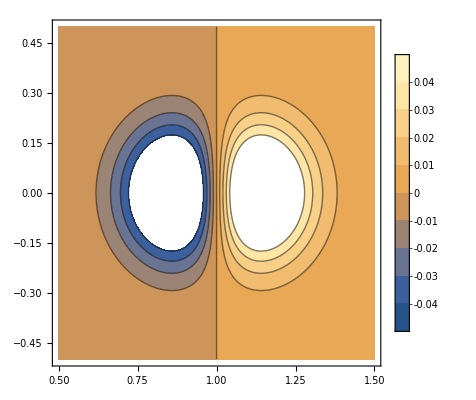

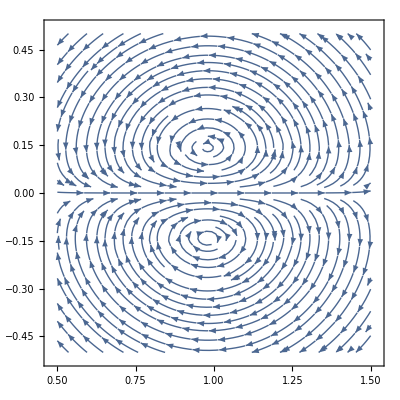

```mathematica
ContourPlot[ψpb/.{Δ->0.2,ϕ->0,R0->1,q0->2/3,b->1},{R,0.5,1.5},{Z,-0.5,0.5},PlotLegends->Automatic,PlotPoints->100]
StreamPlot[{Bpert[[1]],Bpert[[3]]}/.{Δ->0.2,ϕ->0,R0->1,q0->2/3,b->1},{R,0.5,1.5},{Z,-0.5,0.5},StreamPoints->Fine]
```

```mathematica
Bcartpert=TransformedField["Cylindrical"-> "Cartesian", Bpert, {R, ϕ, Z}-> {x, y, z}];
BcartpertFin=Bcartpert/.{R0->1,x->xx[0],y->xx[1],z->xx[2],Δ->width,q0->sf,b->1} // FullSimplify
```

{1/width^2 ⅇ^(-((-1+√(xx[0]^2+xx[1]^2))^2+xx[2]^2)/width^2) xx[0] ((2 xx[0] (width^2-2 xx[2]^2))/((xx[0]^2+xx[1]^2)^2)+(4 xx[1] (-1+√(xx[0]^2+xx[1]^2)) xx[2] √(-xx[0]^2-xx[1]^2+2 √(xx[0]^2+xx[1]^2)-xx[2]^2) (sf+(-1+√(xx[0]^2+xx[1]^2))^2+xx[2]^2))/((xx[0]^2+xx[1]^2)^(5/2))-(2 xx[1] xx[2] (4 (-1+√(xx[0]^2+xx[1]^2)) (xx[0]^2+xx[1]^2-2 √(xx[0]^2+xx[1]^2)+xx[2]^2) (sf+(-1+√(xx[0]^2+xx[1]^2))^2+xx[2]^2)-width^2 √(xx[0]^2+xx[1]^2) (1+sf-6 √(xx[0]^2+xx[1]^2)+3 (xx[0]^2+xx[1]^2)+3 xx[2]^2)))/((xx[0]^2+xx[1]^2)^(5/2) √(-xx[0]^2-xx[1]^2+2 √(xx[0]^2+xx[1]^2)-xx[2]^2))),1/width^2 ⅇ^(-((-1+√(xx[0]^2+xx[1]^2))^2+xx[2]^2)/width^2) ((xx[1] (2 xx[0] (width^2-2 xx[2]^2)+(4 xx[1] (-1+√(xx[0]^2+xx[1]^2)) xx[2] √(-xx[0]^2-xx[1]^2+2 √(xx[0]^2+xx[1]^2)-xx[2]^2) (sf+(-1+√(xx[0]^2+xx[1]^2))^2+xx[2]^2))/(√(xx[0]^2+xx[1]^2))))/((xx[0]^2+xx[1]^2)^2)+(2 xx[0]^2 xx[2] (4 (-1+√(xx[0]^2+xx[1]^2)) (xx[0]^2+xx[1]^2-2 √(xx[0]^2+xx[1]^2)+xx[2]^2) (sf+(-1+√(xx[0]^2+xx[1]^2))^2+xx[2]^2)-width^2 √(xx[0]^2+xx[1]^2) (1+sf-6 √(xx[0]^2+xx[1]^2)+3 (xx[0]^2+xx[1]^2)+3 xx[2]^2)))/((xx[0]^2+xx[1]^2)^(5/2) √(-xx[0]^2-xx[1]^2+2 √(xx[0]^2+xx[1]^2)-xx[2]^2))),1/(width^2 (xx[0]^2+xx[1]^2)^2)2 ⅇ^(-((-1+√(xx[0]^2+xx[1]^2))^2+xx[2]^2)/width^2) (xx[0] (width^2+2 (xx[0]^2+xx[1]^2-√(xx[0]^2+xx[1]^2))) xx[2]-xx[1] (-width^2+2 (-1+√(xx[0]^2+xx[1]^2))^2) √(-xx[0]^2-xx[1]^2+2 √(xx[0]^2+xx[1]^2)-xx[2]^2) (sf+(-1+√(xx[0]^2+xx[1]^2))^2+xx[2]^2))}

```mathematica
FortranForm[BcartpertFin[[1]]]
```

(xx(0)*((2*xx(0)*(width**2 - 2*xx(2)**2))/(xx(0)**2 + xx(1)**2)**2 + 
     -      (4*xx(1)*(-1 + Sqrt(xx(0)**2 + xx(1)**2))*xx(2)*Sqrt(-xx(0)**2 - xx(1)**2 + 2*Sqrt(xx(0)**2 + xx(1)**2) - xx(2)**2)*
     -         (sf + (-1 + Sqrt(xx(0)**2 + xx(1)**2))**2 + xx(2)**2))/(xx(0)**2 + xx(1)**2)**2.5 - 
     -      (2*xx(1)*xx(2)*(4*(-1 + Sqrt(xx(0)**2 + xx(1)**2))*(xx(0)**2 + xx(1)**2 - 2*Sqrt(xx(0)**2 + xx(1)**2) + xx(2)**2)*
     -            (sf + (-1 + Sqrt(xx(0)**2 + xx(1)**2))**2 + xx(2)**2) - 
     -           width**2*Sqrt(xx(0)**2 + xx(1)**2)*(1 + sf - 6*Sqrt(xx(0)**2 + xx(1)**2) + 3*(xx(0)**2 + xx(1)**2) + 3*xx(2)**2)))/
     -       ((xx(0)**2 + xx(1)**2)**2.5*Sqrt(-xx(0)**2 - xx(1)**2 + 2*Sqrt(xx(0)**2 + xx(1)**2) - xx(2)**2))))/
     -  (E**(((-1 + Sqrt(xx(0)**2 + xx(1)**2))**2 + xx(2)**2)/width**2)*width**2)

```mathematica
FortranForm[BcartpertFin[[2]]]
```

((xx(1)*(2*xx(0)*(width**2 - 2*xx(2)**2) + (4*xx(1)*(-1 + Sqrt(xx(0)**2 + xx(1)**2))*xx(2)*
     -            Sqrt(-xx(0)**2 - xx(1)**2 + 2*Sqrt(xx(0)**2 + xx(1)**2) - xx(2)**2)*(sf + (-1 + Sqrt(xx(0)**2 + xx(1)**2))**2 + xx(2)**2))/
     -          Sqrt(xx(0)**2 + xx(1)**2)))/(xx(0)**2 + xx(1)**2)**2 + 
     -    (2*xx(0)**2*xx(2)*(4*(-1 + Sqrt(xx(0)**2 + xx(1)**2))*(xx(0)**2 + xx(1)**2 - 2*Sqrt(xx(0)**2 + xx(1)**2) + xx(2)**2)*
     -          (sf + (-1 + Sqrt(xx(0)**2 + xx(1)**2))**2 + xx(2)**2) - 
     -         width**2*Sqrt(xx(0)**2 + xx(1)**2)*(1 + sf - 6*Sqrt(xx(0)**2 + xx(1)**2) + 3*(xx(0)**2 + xx(1)**2) + 3*xx(2)**2)))/
     -     ((xx(0)**2 + xx(1)**2)**2.5*Sqrt(-xx(0)**2 - xx(1)**2 + 2*Sqrt(xx(0)**2 + xx(1)**2) - xx(2)**2)))/
     -  (E**(((-1 + Sqrt(xx(0)**2 + xx(1)**2))**2 + xx(2)**2)/width**2)*width**2)

```mathematica
FortranForm[BcartpertFin[[3]]]
```

(2*(xx(0)*(width**2 + 2*(xx(0)**2 + xx(1)**2 - Sqrt(xx(0)**2 + xx(1)**2)))*xx(2) - 
     -      xx(1)*(-width**2 + 2*(-1 + Sqrt(xx(0)**2 + xx(1)**2))**2)*Sqrt(-xx(0)**2 - xx(1)**2 + 2*Sqrt(xx(0)**2 + xx(1)**2) - xx(2)**2)*
     -       (sf + (-1 + Sqrt(xx(0)**2 + xx(1)**2))**2 + xx(2)**2)))/
     -  (E**(((-1 + Sqrt(xx(0)**2 + xx(1)**2))**2 + xx(2)**2)/width**2)*width**2*(xx(0)**2 + xx(1)**2)**2)

If you have infinite time, here’s the divergence...

```mathematica
Div[Bcartpert,{x,y,z}] // FullSimplify
```

0